# Trivial Equilibria Stability Analysis

```mathematica
ClearAll[phi,psi,A,B,phiPrime,psiPrime,APrime,BPrime,dA,dB,p,b,m,s];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M ={{dA*(1-B)+p*B,dA*A,0,0},{dB*B,dB*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}};
dA = ϵ
dB =ϵ
(*Vector on the right-hand side*)
RHS:={-s*phi-F[A,B],-s*psi-G[A,B],phi,psi};
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
Minv = FullSimplify[Inverse[M]] // MatrixForm
LHS:=Inverse[M].RHS;
(*Solve for derivatives when {phi',psi',A',B'}=0*)
EquilibriaEquation := LHS == {0,0,0,0};
equilibria = Solve[EquilibriaEquation, {phi, psi, A, B}];
(*Returning the trivial equilibria(0,0,0,0)*)
trivialEquilibrium := equilibria [[1]]
```

ϵ

ϵ

((-b B+ϵ-A (b+ϵ))/(-A B ϵ^2+(b (A+B)+(-1+A) ϵ) (-B p+(-1+B) ϵ)) | (A ϵ)/(b B (A+B) p-b (-1+B) (A+B) ϵ+(-1+A) B p ϵ+(-1+A+B) ϵ^2) | 0 | 0
-(B ϵ)/(-A B ϵ^2+(b (A+B)+(-1+A) ϵ) (-B p+(-1+B) ϵ)) | (B (p-ϵ)+ϵ)/(-A B ϵ^2+(b (A+B)+(-1+A) ϵ) (-B p+(-1+B) ϵ)) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Series[({{(-b B+ϵ-A (b+ϵ))/(-A B ϵ^2+(b (A+B)+(-1+A) ϵ) (-B p+(-1+B) ϵ)), (A ϵ)/(b B (A+B) p-b (-1+B) (A+B) ϵ+(-1+A) B p ϵ+(-1+A+B) ϵ^2), 0, 0}, {-(B ϵ)/(-A B ϵ^2+(b (A+B)+(-1+A) ϵ) (-B p+(-1+B) ϵ)), (B (p-ϵ)+ϵ)/(-A B ϵ^2+(b (A+B)+(-1+A) ϵ) (-B p+(-1+B) ϵ)), 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}),{ϵ,0,2}] //MatrixForm
```

(1/(B p)+((-1+B) ϵ)/(B^2 p^2)+((A b+b B-2 A b B-2 b B^2+A b B^2+b B^3-A B^2 p) ϵ^2)/(b B^3 (A+B) p^3)+O[ϵ]^3 | (A ϵ)/(b B (A+B) p)-(A (-b (-1+B) (A+B)+(-1+A) B p) ϵ^2)/(b^2 B^2 (A+B)^2 p^2)+O[ϵ]^3 | 0 | 0
ϵ/(b (A+B) p)+((b (-1+B) (A+B)-(-1+A) B p) ϵ^2)/(b^2 B (A+B)^2 p^2)+O[ϵ]^3 | -1/(b (A+B))+((-1+A) ϵ)/(b^2 (A+B)^2)+((A^2 b+A b B-p+2 A p-A^2 p) ϵ^2)/(b^3 (A+B)^3 p)+O[ϵ]^3 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*Find the Jacobian of the system *)
JacMatrix := D[LHS,{{phi,psi,A,B}}] ;
ParamReplacements := {D->0.1,p->0.2,dA->0.01, dB->0.01 ,m->0.001};
NumJacMatrix := JacMatrix /. ParamReplacements;
Minv /. ParamReplacements
```

((0.01-A (0.01+b)-b B)/(-0.0001 A B+(0.01 (-1+B)-0.2 B) (0.01 (-1+A)+b (A+B))) | -(0.01 A)/(-0.0001 A B+(0.01 (-1+B)-0.2 B) (0.01 (-1+A)+b (A+B))) | 0 | 0
-(0.01 B)/(-0.0001 A B+(0.01 (-1+B)-0.2 B) (0.01 (-1+A)+b (A+B))) | (0.01+0.19 B)/(-0.0001 A B+(0.01 (-1+B)-0.2 B) (0.01 (-1+A)+b (A+B))) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
TrivialEqJacob := JacMatrix /. trivialEquilibrium
```

```mathematica
EigenTrivial := Eigenvalues[TrivialEqJacob]
```

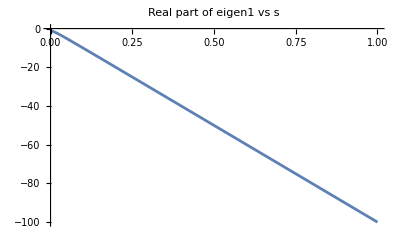

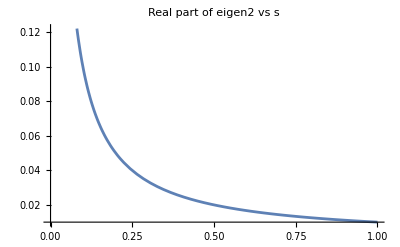

-Graphics3D-

-Graphics3D-

```mathematica
eigen1[b_,s_]:= EigenTrivial[[1]] /. ParamReplacements;
eigen2[b_,s_]:= EigenTrivial[[2]] /. ParamReplacements;
eigen3[b_,s_]:= EigenTrivial[[3]] /. ParamReplacements;
eigen4[b_,s_]:= EigenTrivial[[4]] /. ParamReplacements;

Plot[Re[eigen1[b,s]],{s,0,1},PlotLabel->"Real part of eigen1 vs s"]
Plot[Re[eigen2[b,s]],{s,0,1},PlotLabel->"Real part of eigen2 vs s"]
Plot3D[
 Re[eigen3[b, s]],
 {b, -1, 1}, {s, 0, 10},
 PlotLabel -> "Real part of eigen3 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen3]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]

Plot3D[
 Re[eigen4[b, s]],
 {b, -1, 1}, {s, 0, 10},
 PlotLabel -> "Real part of eigen4 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen4]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
```